```mathematica
(*Dialog prompt to fix in/out paths.  Can be replaced with direct path input later*)
id=ChoiceDialog[
"It's dangerous to go alone! Who are you and your computer companion?",{"Sam & Cuchulain"-> "Sam", "Sherwood & Ganon"->"Sherwood","Someone new"->"Other"}];
(*Sets the paths based on the machine pick.  The paths are global*)
 Which[id=="Sam",
 inpath="G:\\My Drive\\Physics\\Neutrino Oscillation Research\\Fast Conversions\\lotsadata.tar\\lotsadata\\lotsadata\\";
 outpath="G:\\My Drive\\Physics\\Neutrino Oscillation Research\\Fast Conversions\\stability_data\\";
 ,
 id=="Sherwood",
 inpath="/mnt/data/SamFlynn/lotsadata/";
 outpath="/mnt/data/SamFlynn/stability_data/";
 ,
 id=="Other",
 inpath = SystemDialogInput["Directory",WindowTitle-> "Choose the folder containing the data set"];
 outpath = inpath<>"out\\";
 ];
 (*Want to implements toggle grid here to pick between the mass models and time slices.  It's easy, but definitely not a priority*)
(*
filename = "15Msun_50ms_DO";
infile = inpath<>filename<>".h5";
outfolder = outpath<>filename;
*)
(*Note: this used to contain a variable called "out_path". Be careful with the underscores; in Mathematica they are either function inputs or patterns.  If the font turn green, that's why.*)
(*Constants*)
```

```mathematica
SetDirectory["C:\\Users\\Sam\\Documents\\GitHub\\stability_tools"]
<<"StabilityPackage`"
```

C:\Users\Sam\Documents\GitHub\stability_tools

```mathematica
?stabilityMatrix
?getEquations
?buildHamiltonians
```

#### Checks:

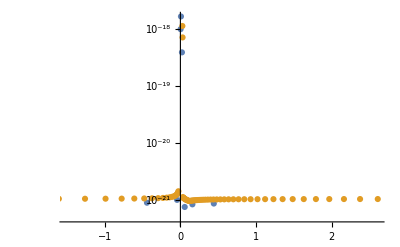

TestResultObject[…]

```mathematica
OldData={{2.61019*10^-17, 1.12835*10^-18}, {2.8674*10^-17, 
  7.11518*10^-19}, {3.14996*10^-17, 1.13532*10^-21}, {3.46036*10^-17, 
  1.12664*10^-21}, {3.80135*10^-17, 1.11669*10^-21}, {4.17594*10^-17, 
  1.10578*10^-21}, {4.58744*10^-17, 1.09417*10^-21}, {5.03949*10^-17, 
  1.08207*10^-21}, {5.53608*10^-17, 1.06968*10^-21}, {6.08162*10^-17, 
  1.05717*10^-21}, {6.68091*10^-17, 1.04469*10^-21}, {7.33925*10^-17, 
  1.03234*10^-21}, {8.06247*10^-17, 1.02023*10^-21}, {8.85695*10^-17, 
  1.00844*10^-21}, {9.72973*10^-17, 9.97028*10^-22}, {1.06885*10^-16, 
  9.86047*10^-22}, {1.17418*10^-16, 9.75532*10^-22}, {1.28988*10^-16, 
  9.78299*10^-22}, {1.41699*10^-16, 9.85668*10^-22}, {1.55662*10^-16, 
  9.92358*10^-22}, {1.71001*10^-16, 9.98434*10^-22}, {1.87852*10^-16, 
  1.00395*10^-21}, {2.06363*10^-16, 1.00897*10^-21}, {2.26698*10^-16, 
  1.01353*10^-21}, {2.49037*10^-16, 1.01767*10^-21}, {2.73577*10^-16, 
  1.02144*10^-21}, {3.00536*10^-16, 1.02487*10^-21}, {3.30151*10^-16, 
  1.02798*10^-21}, {3.62685*10^-16, 1.03082*10^-21}, {3.98424*10^-16, 
  1.03339*10^-21}, {4.37685*10^-16, 1.03574*10^-21}, {4.80815*10^-16, 
  1.03787*10^-21}, {5.28195*10^-16, 1.03981*10^-21}, {5.80244*10^-16, 
  1.04157*10^-21}, {6.37422*10^-16, 1.04318*10^-21}, {7.00235*10^-16, 
  1.04464*10^-21}, {7.69236*10^-16, 1.04597*10^-21}, {8.45038*10^-16, 
  1.04718*10^-21}, {9.28309*10^-16, 1.04828*10^-21}, {1.01979*10^-15, 
  1.04928*10^-21}, {1.12028*10^-15, 1.05019*10^-21}, {1.23067*10^-15, 
  1.05102*10^-21}, {1.35194*10^-15, 1.05178*10^-21}, {1.48516*10^-15, 
  1.05247*10^-21}, {1.63151*10^-15, 1.05309*10^-21}, {1.79228*10^-15, 
  1.05366*10^-21}, {1.9689*10^-15, 1.05418*10^-21}, {2.16292*10^-15, 
  1.05465*10^-21}, {2.37605*10^-15, 1.05508*10^-21}, {2.61019*10^-15, 
  1.05547*10^-21}, {-2.61019*10^-17, 1.44396*10^-21}, {-3.3261*10^-17,
   1.36214*10^-21}, {-4.23837*10^-17, 
  1.29781*10^-21}, {-5.40084*10^-17, 
  1.24715*10^-21}, {-6.88216*10^-17, 
  1.20722*10^-21}, {-8.76976*10^-17, 
  1.17574*10^-21}, {-1.11751*10^-16, 
  1.15093*10^-21}, {-1.42401*10^-16, 
  1.13139*10^-21}, {-1.81459*10^-16, 1.116*10^-21}, {-2.31228*10^-16, 
  1.10389*10^-21}, {-2.94648*10^-16, 
  1.09436*10^-21}, {-3.75463*10^-16, 
  1.08687*10^-21}, {-4.78443*10^-16, 
  1.08098*10^-21}, {-6.09668*10^-16, 
  1.07635*10^-21}, {-7.76884*10^-16, 
  1.07272*10^-21}, {-9.89964*10^-16, 
  1.06986*10^-21}, {-1.26149*10^-15, 
  1.06762*10^-21}, {-1.60748*10^-15, 
  1.06586*10^-21}, {-2.04837*10^-15, 
  1.06448*10^-21}, {-2.61019*10^-15, 1.06339*10^-21}};
kdebug=Block[{data,ri=200,testE=20,hi=-1,k=0,kvar},
file=inpath<>"1D_withV_withPairBrems_DO.h5";
(*SCalcScale[ImportData[inpath<>file<>".h5"],ri,testE,hi,0][[3]]//MatrixForm*)
(*buildkGrid[ImportData[inpath<>file<>".h5"],ri,testE,hi,40]*)
kAdapt[file,ri,ri,testE,hi,10]
];
ListLogPlot[{Transpose@{kdebug[[All,2]],kdebug[[All,3]]},OldData},ImageSize-> Scaled[0.65]]

(*2x2 matrix check*)
get2bdata[]:=Block[{S2ba,S2b,data2b,fakeEn,c,h,hbar,Gf,everg,Geverg,munits},
c=2.99792458 10^10; (* cm/s*)
h=6.6260755 10^-27; (*erg s*)
hbar = h/(2 Pi); (*erg s*)
Gf=1.1663787 10^-5; (*GeV^-2*)
everg=1.60218 10^-12; (* convert eV to ergs*)
Geverg = everg*10^9; (* convert GeV to ergs *)
munits=Sqrt[2] (Gf/Geverg^2 )(hbar c)^3; (*Sqrt[2] Gf in erg cm^3*)
data2b=
 Association[
"muss"-> {-1,0,1},
"matters"-> 0.,
"Yes"-> 0.,
"mids"-> {-Pi,Pi},
"freqs"->{0,2},
"lotsodo"-> {{{{ (1+a),0.},{0.,0.}}},{{{0.,0.},{ (1-a),0.}}}},
 "freqmid"-> {1},
 "munits"-> munits
]
];
build2bMatrix[]:=Block[{fakeEn,S2ba,S2b},
fakeEn=6.080273099999999*^-22; (*MeV input, output in ergs*)
S2ba=stabilityMatrix[get2bdata[],getEquations[get2bdata[],fakeEn,-1,0.,"xflavor"-> False],"xflavor"-> False];
S2b={{S2ba[[1,1]],S2ba[[1,4]]},{S2ba[[4,1]],S2ba[[4,4]]}};
Return[S2b]
];

Ωch[k_,μch_,a_,ω_]=2 a μch+√((2 a μch)^2+ω(ω-4 μch));
evtest=Eigenvalues[build2bMatrix[]/.{a-> 0.1}][[2]];
vt=VerificationTest[
Abs[Im[Ωch[0.,N[(2.0929595558280123*^-21)/2],0.1,0.1]]]-Abs[Im[evtest]]<10^-3
,TestID-> "2 Beam Growth Rate"]
```

## Plotting Functions :

```mathematica
conplot[pts_,title_,klower_,kupper_,export_]:=Block[{ppts,plotout},
ppts=Transpose@{pts[[All,1]]/10^5,pts[[All,2]]/pts[[All,4]],pts[[All,3]]/pts[[All,4]]};
plotout=ListContourPlot[ppts,PlotLegends-> Automatic,PlotRange-> {All,{klower,kupper},All},MaxPlotPoints-> Infinity,FrameLabel->{"Radius (km)","k/μ",None,"Ω/μ"},PlotLabel-> title,ImageSize-> Scaled[0.4]];
If[export==1,Export[outpath<>title<>"_contourplot.pdf",plotout]];
Return[plotout];
];

conplotauto[pts_,title_,export_]:=Block[{ppts,plotout},
ppts=Transpose@{pts[[All,1]]/10^5,pts[[All,2]]/pts[[All,4]],pts[[All,3]]/pts[[All,4]]};
plotout=ListContourPlot[ppts,PlotLegends-> Automatic,PlotRange-> {All,All,All},MaxPlotPoints-> Infinity,FrameLabel->{"Radius (km)","k/μ",None,"Ω/μ"},PlotLabel-> title,ImageSize-> Scaled[0.4]];
If[export==1,Export[outpath<>title<>"_contourplot.pdf",plotout]];
Return[plotout];
];

pointplot[pts_,title_,export_]:=Block[{ppts,plotout},
ppts=Transpose@{pts[[All,1]],pts[[All,2]],pts[[All,3]]/pts[[All,4]]};
plotout=ListPointPlot3D[ppts,AxesLabel-> {"radius (cm)","k (erg)","Im[Ω] (erg)"},PlotLabel-> title,PlotRange->{All,All,All},ImageSize->Scaled[0.8],TicksStyle-> Directive[16],LabelStyle-> Directive[18],ColorFunction-> "Rainbow",PlotLegends-> Automatic,PlotLabel-> title];
If[export==1,Export[outpath<>title<>"_pointplot.pdf",plotout]];
Return[plotout];
];
```